This is a supplementary Mathematica notebook for the paper “Fractonic solids” available at https://arxiv.org/abs/2406.07334.
Here we compute the quasi-normal modes of a charged black brane in the holographic model for fractonic solids.

## Ordinary charged holography

For comparison, let us first consider the diffusive QNM in ordinary charged holography. We start with the differential equation

```mathematica
fVal[z_,d_,z0_]=1-z^(d+1)/z0^(d+1);
DE[ⅈω_,k_,z_,d_,z0_]=(1/z^(d-2)D[(z^(d-2)f[z,d,z0]a'[z]), z]+ⅈω(a'[z]+1/z^(d-2)D[(z^(d-2)a[z]), z])-k^2 a[z])/.f->fVal//Simplify;
```

Perform asymptotic expansions

```mathematica
expansion=5;
aAnsUV[z_]=Sum[aUV[n] z^n,{n,0,expansion}];
aAnsIR[z_,z0_]=Sum[aIR[n](z0-z)^n,{n,0,expansion}];
BCUV[ⅈω_,k_,d_,z0_]:=z DE[ⅈω,k,z,d,z0]/.a->aAnsUV//#+O[z]^expansion&//Solve[#==0,Table[aUV[n],{n,1,expansion}]]&//Simplify//{a->Function[z,aAnsUV[z]//Evaluate]}/.#⟦1⟧/.aUV[0]->1/.aUV[3-d]->0&;
BCIR[ⅈω_,k_,a0_,d_,z0_]:=DE[ⅈω,k,z,d,z0]/.a->Function[z,aAnsIR[z,z0]]/.z->z0+δz//#+O[δz]^expansion&//Solve[#==0,Table[aIR[n],{n,1,expansion}]]&//Simplify//{a->Function[z,aAnsIR[z,z0]//Evaluate]}/.#⟦1⟧/.aIR[0]->a0&;
```

Find numerical solutions shooting from the boundary and the horizon

```mathematica
ϵ=10^-5;
zMid=1/2;
SolUV[ⅈω_,k_,d_,z0_]:=NDSolve[{DE[ⅈω,k,zz,d,z0]==0,a[ϵ]==(a[ϵ]/.BCUV[ⅈω,k,d,z0]),a'[ϵ]==(a'[ϵ]/.BCUV[ⅈω,k,d,z0])},a,{zz,ϵ,zMid}]
SolIR[ⅈω_,k_,a0_,d_,z0_]:=NDSolve[{DE[ⅈω,k,zz,d,z0]==0,a[1-ϵ]==(a[1-ϵ]/.BCIR[ⅈω,k,a0,d,z0]),a'[1-ϵ]==(a'[1-ϵ]/.BCIR[ⅈω,k,a0,d,z0])},a,{zz,1-ϵ,zMid}]
```

Match the solutions in the middle

```mathematica
ⅈdisp[k_,d_,z0_]:=Module[{roots},
roots=FindRoot[{(a[0.5]/.SolUV[ⅈω,k,d,z0])==(a[0.5]/.SolIR[ⅈω,k,a0,d,z0]),(a'[0.5]/.SolUV[ⅈω,k,d,z0])==(a'[0.5]/.SolIR[ⅈω,k,a0,d,z0])}//Evaluate,{a0,1},{ⅈω,0}]//Quiet;
{ⅈω,a0}/.roots
]
```

Try plotting the matched solution

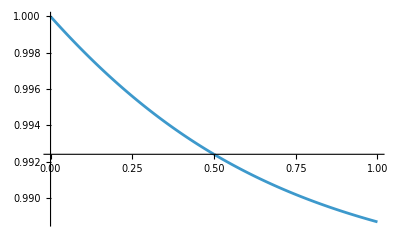

```mathematica
k=0.2;d=3;z0=1;
{ⅈω,a0}=ⅈdisp[k,d,z0];
Show[{
Plot[a[u]/.SolUV[ⅈω,k,d,z0],{u,ϵ,zMid}],
Plot[a[u]/.SolIR[ⅈω,k,a0,d,z0],{u,zMid,1-ϵ}]
},PlotRange->All]
ClearAll[k,d,z0,ⅈω,a0]
```

Find the dispersion relations, best fit, and diffusive ansatz

0.499998 k^2+0.086699 k^4+0.0251614 k^6+0.0111424 k^8

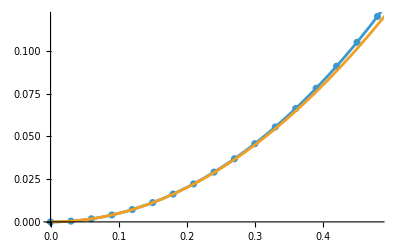

```mathematica
d=3;z0=1;
dispsQ0=Table[{k,ⅈdisp[k,d,z0]⟦1⟧},{k,0,0.5,0.03}];
fit[k_]=Fit[dispsQ0,{k^2,k^4,k^6,k^8},k]
Show[{ListPlot[dispsQ0],Plot[{fit[k],z0/(d-1)k^2},{k,0,1}]}]
ClearAll[d,z0]
```

The parametric form z0/(d-1) can be obtained by repeating this calculation for different values of parameters.

## Crystal-dipole holography

Let us now consider the sub-diffusive QNM in crystal-dipole holography. We start with the differential equations

```mathematica
fVal[z_,d_,z0_]=1-z^(d+1)/z0^(d+1);
DE1[ⅈω_,k_,z_,d_,z0_,λ_]=(1/z^(d-2)D[(z^(d-2)f[z,d,z0]a'[z]), z]+ⅈω(a'[z]+1/z^(d-2)D[(z^(d-2)a[z]), z])-k^2 a[z]+λ k^2 b[z])/.f->fVal//Simplify;
DE2[ⅈω_,k_,z_,d_,z0_,λ_]=(1/z^(d-2)D[(z^(d-2)f[z,d,z0]b'[z]), z]+ⅈω(b'[z]+1/z^(d-2)D[(z^(d-2)b[z]), z])-k^2 b[z]-(λ b[z]-a[z]))/.f->fVal//Simplify;
```

We have redefined b-> ⅈk b compared to the main text to keep the differential equations real.

Perform asymptotic expansions

```mathematica
expansion=5;
aAnsUV[z_]=Sum[aUV[n] z^n,{n,0,expansion}];
bAnsUV[z_]=Sum[bUV[n] z^n,{n,0,expansion}];
aAnsIR[z_,z0_]=Sum[aIR[n](z0-z)^n,{n,0,expansion}];
bAnsIR[z_,z0_]=Sum[bIR[n](z0-z)^n,{n,0,expansion}];
BCUV[ⅈω_,k_,bx_,d_,z0_,λ_]:=z{DE1[ⅈω,k,z,d,z0,λ],DE2[ⅈω,k,z,d,z0,λ]}/.a->aAnsUV/.b->bAnsUV//#+O[z]^expansion&//Solve[#=={0,0},Table[{aUV[n],bUV[n]},{n,1,expansion}]//Flatten]&//{a->Function[z,aAnsUV[z]//Evaluate],b->Function[z,bAnsUV[z]//Evaluate]}/.#⟦1⟧/.aUV[0]->1/.bUV[0]->bx&;
BCIR[ⅈω_,k_,a0_,b0_,d_,z0_,λ_]:={DE1[ⅈω,k,z,d,z0,λ],DE2[ⅈω,k,z,d,z0,λ]}/.a->Function[z,aAnsIR[z,z0]]/.b->Function[z,bAnsIR[z,z0]]/.z->z0-δz//#+O[δz]^expansion&//Solve[#=={0,0},Table[{aIR[n],bIR[n]},{n,1,expansion}]//Flatten]&//Simplify//{a->Function[z,aAnsIR[z,z0]//Evaluate],b->Function[z,bAnsIR[z,z0]//Evaluate]}/.#⟦1⟧/.aIR[0]->a0/.bIR[0]->b0&;
```

Find numerical solutions shooting from the boundary and the horizon

```mathematica
ϵ=10^-5;
zMid=1/2;
SolUV[ⅈω_,k_,bx_,d_,z0_,λ_]:=NDSolve[{DE1[ⅈω,k,zz,d,z0,λ]==0,DE2[ⅈω,k,zz,d,z0,λ]==0,a[ϵ]==(a[ϵ]/.BCUV[ⅈω,k,bx,d,z0,λ]),a'[ϵ]==(a'[ϵ]/.BCUV[ⅈω,k,bx,d,z0,λ]),b[ϵ]==(b[ϵ]/.BCUV[ⅈω,k,bx,d,z0,λ]),b'[ϵ]==(b'[ϵ]/.BCUV[ⅈω,k,bx,d,z0,λ])},{a,b},{zz,ϵ,zMid}]
SolIR[ⅈω_,k_,a0_,b0_,d_,z0_,λ_]:=NDSolve[{DE1[ⅈω,k,zz,d,z0,λ]==0,DE2[ⅈω,k,zz,d,z0,λ]==0,a[1-ϵ]==(a[1-ϵ]/.BCIR[ⅈω,k,a0,b0,d,z0,λ]),a'[1-ϵ]==(a'[1-ϵ]/.BCIR[ⅈω,k,a0,b0,d,z0,λ]),b[1-ϵ]==(b[1-ϵ]/.BCIR[ⅈω,k,a0,b0,d,z0,λ]),b'[1-ϵ]==(b'[1-ϵ]/.BCIR[ⅈω,k,a0,b0,d,z0,λ])},{a,b},{zz,1-ϵ,zMid}]
```

Match the solutions in the middle

```mathematica
ⅈdisp[k_,d_,z0_,λ_]:=Module[{roots},
roots=FindRoot[{
(a[0.5]/.SolUV[ⅈω,k,bx,d,z0,λ])==(a[0.5]/.SolIR[ⅈω,k,a0,b0,d,z0,λ]),
(a'[0.5]/.SolUV[ⅈω,k,bx,d,z0,λ])==(a'[0.5]/.SolIR[ⅈω,k,a0,b0,d,z0,λ]),
(b[0.5]/.SolUV[ⅈω,k,bx,d,z0,λ])==(b[0.5]/.SolIR[ⅈω,k,a0,b0,d,z0,λ]),
(b'[0.5]/.SolUV[ⅈω,k,bx,d,z0,λ])==(b'[0.5]/.SolIR[ⅈω,k,a0,b0,d,z0,λ])
}//Evaluate,{ⅈω,0},{a0,1},{b0,1},{bx,1}]//Quiet;
{ⅈω,a0,b0,bx}/.roots
]
```

Try plotting the matched solution

{0.0000490271,0.999972,0.990168,0.990195}

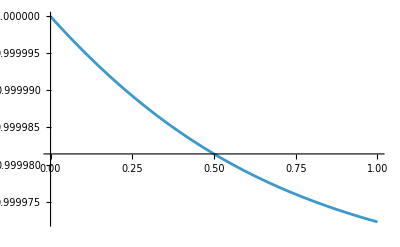

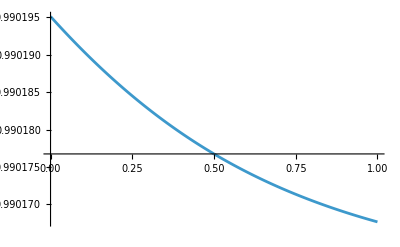

```mathematica
k=0.1;d=3;z0=1;λ=1;
{ⅈωX,a0X,b0X,bxX}=ⅈdisp[k,d,z0,λ]
Show[{
Plot[a[z]/.SolUV[ⅈωX,k,bxX,d,z0,λ]//Evaluate,{z,ϵ,zMid}],
Plot[a[z]/.SolIR[ⅈωX,k,a0X,b0X,d,z0,λ]//Evaluate,{z,zMid,1-ϵ}]
},PlotRange->All]
Show[{
Plot[b[z]/.SolUV[ⅈωX,k,bxX,d,z0,λ]//Evaluate,{z,ϵ,zMid}],
Plot[b[z]/.SolIR[ⅈωX,k,a0X,b0X,d,z0,λ]//Evaluate,{z,zMid,1-ϵ}]
},PlotRange->All]
ClearAll[k,ⅈωX,d,z0,λ,a0X,b0X,bxX]
```

0.491894 k^4-0.803454 k^6+0.881476 k^8

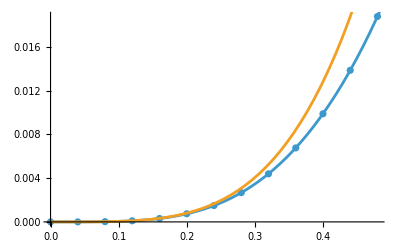

```mathematica
d=3;z0=1;λ=1;
dispsQ1=Table[{k,ⅈdisp[k,d,z0,λ]⟦1⟧},{k,0,0.5,0.04}];
fit[k_]=Fit[dispsQ1,{k^4,k^6,k^8},k]
Show[{ListPlot[dispsQ1],Plot[{fit[k],(z0/λ)/(d-1)k^4},{k,0,0.5}]}]
ClearAll[d,z0,λ]
```

The parametric form (z0/λ)/(d-1) can be obtained by repeating this calculation for different values of parameters.
The data differs from the sub-diffusive ansatz at larger values of k due to higher-order corrections.

## Plotting the datasets together

```mathematica
dispsQ0
dispsQ1
```

{{0.,0.},{0.03,0.000450073},{0.06,0.00180113},{0.09,0.0040557},{0.12,0.00721805},{0.15,0.0112941},{0.18,0.0162918},{0.21,0.0222207},{0.24,0.0290924},{0.27,0.0369206},{0.3,0.0457211},{0.33,0.055512},{0.36,0.0663138},{0.39,0.0781499},{0.42,0.0910463},{0.45,0.105032},{0.48,0.120141}}

{{0.,0.},{0.04,1.27621×10^-6},{0.08,0.0000202223},{0.12,0.000100804},{0.16,0.000311939},{0.2,0.00074195},{0.24,0.00149228},{0.28,0.0026715},{0.32,0.00439024},{0.36,0.00675738},{0.4,0.00987756},{0.44,0.0138498},{0.48,0.0187673}}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"monopole_qnm.csv"}],dispsQ0]
Export[FileNameJoin[{NotebookDirectory[],"dipole_qnm.csv"}],dispsQ1]
```

/Users/akash/Documents/Wolfram Mathematica/CrystalFractons/final/monopole_qnm.csv

/Users/akash/Documents/Wolfram Mathematica/CrystalFractons/final/dipole_qnm.csv

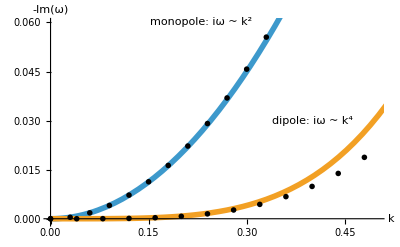

```mathematica
Show[{
Plot[{1/2 k^2,1/2 k^4},{k,0,0.6},PlotStyle->Thickness[0.01]],
ListPlot[{dispsQ0,dispsQ1},PlotMarkers->"OpenMarkers",PlotStyle->Black]
},PlotRange->{{0,0.5},{-0.001,0.06}},AspectRatio->1/GoldenRatio,AxesLabel->{Style["k",16],Style["-Im(ω)",16]},BaseStyle->12,Epilog->{Style[Text["monopole: iω ~ k^2",{.23,.06}],16],Style[Text["dipole: iω ~ k^4",{.4,.03}],16]}]
```